```mathematica
(*Avtomatsko shranjevanje notebook-a*)
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

# 1. kviz 2025/26 [20 točk]

Naloge rešujte samostojno. Uporaba naravnega jezika ni dovoljena, razen kjer je to eksplicitno zapisano.

## 1. naloga [2 točki]

Napišite funkcijo ‘fun’, ki sprejme naravno število n in v primeru, da ima n sodo število števk, vrne njegovo zadnjo števko, v primeru, da ima liho število števk pa njegovo srednjo števko. Na primer, ‘fun[1234]’ vrne ‘4’, ‘fun[12345]’ pa ‘3’. Uporabite lahko funkcijo ‘IntegerDigits’.

```mathematica
fun[n_]:=If[
EvenQ[Length[IntegerDigits[n]]],
Last[IntegerDigits[n]],
IntegerDigits[n][[(Length[IntegerDigits[n]]+1)/2]]]
```

```mathematica
fun[1234]
fun[12345]
```

4

3

## 2. naloga [10 točk]

a) Definirajte funkciji ) in   . Funkciji f in g narišite v isti koordinatni sistem na intervalu [0,15].

```mathematica
f[x_?NumericQ]:=Log[10, (x^4+5)/(x^3-3)-3](*brez numeric.08Q mi ne reši FindRooot*)
g[x_?NumericQ]:=1/(x-3)
```

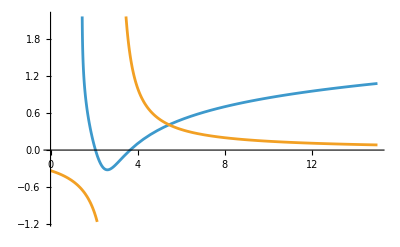

```mathematica
Plot[{f[x],g[x]},{x,0,15}]
```

b)  Določite presečišče funkcij f in g (tj. tisto realno število x, da velja f(x) = g(x)). Rezultat izpišite numerično. Z uporabo funkcije ‘Piecewise’ narišite graf funkcije na [0,15], ki je levo od presečišča enaka funkciji f, desno od presečišča pa funkciji g.

```mathematica
FindRoot[f[x]==g[x],
		{x,5}
		]
```

{x→5.43715}

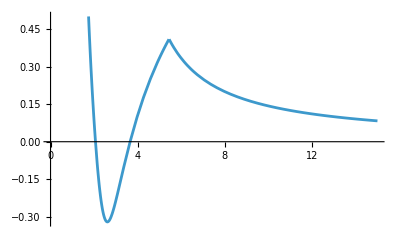

```mathematica
Plot[Piecewise[{
{f[x], x<5.437152394828013},
{g[x], x>5.437152394828013}
}],
{x,0,15}]
```

c) Definirajte funkcijo h s predpisom  in seznam ‘sez’ dolžine 41, ki vsebuje numerične vrednosti funkcije h v točkah x=10,11,12,...,50. Nato definirajte še seznam ‘sez3’, ki vsebuje le tiste elemente iz seznama ‘sez’, katerih celi del je deljiv s 3.

```mathematica
h[x_]:=10f[x]-g[x]
```

```mathematica
sez = Table[N[h[x+9]],{x,41}]
```

{8.32985,8.92141,9.44277,9.9087,10.3298,10.7138,11.0668,11.3934,11.6972,11.9812,12.2477,12.4989,12.7364,12.9616,13.1757,13.3798,13.5747,13.7612,13.9401,14.1119,14.2772,14.4364,14.59,14.7383,14.8817,15.0206,15.1552,15.2857,15.4124,15.5355,15.6552,15.7717,15.8852,15.9958,16.1036,16.2088,16.3116,16.4119,16.51,16.606,16.6998}

```mathematica
sez3 = Select[sez,Mod[IntegerPart[#],3 ]== 0&]
```

{9.44277,9.9087,12.2477,12.4989,12.7364,12.9616,15.0206,15.1552,15.2857,15.4124,15.5355,15.6552,15.7717,15.8852,15.9958}

d) Pobrišite vrednosti spremenljivk ‘f’,’g’,’h’ in ‘sez’. Nato napišite kodo v eni vrstici, ki bo vrnila seznam z enakimi elementi, kot v točki c) seznam ‘sez3’. Pri tem ne definirajte nobenih novih spremenljivk.

```mathematica
Clear[f,g,h,sez]
```

```mathematica
Select[Table[
N[10Log[10, (x^4+5)/(x^3-3)-3]-1/(x-3)]/.x->i+9, 
{i,41}],
Mod[IntegerPart[#],3 ]== 0&]
```

{9.44277,9.9087,12.2477,12.4989,12.7364,12.9616,15.0206,15.1552,15.2857,15.4124,15.5355,15.6552,15.7717,15.8852,15.9958}

e) Definirajte anonimno funkcijo h (s parametrom #) s predpisom . Izračunajte h(2,3) in narišite graf funkcije h na območju [-5,5]x[-5,5].

```mathematica
h = (#1^2-#2^3)/5&;
h[2,3]
Plot3D[h[x,y],{x,-5,5},{y,-5,5}]
```

-23/5

-Graphics3D-

f) Narišite spodnjo sliko: rumen trikotnik s črtkanim črnim robom (oglišča (0,0), (2,-1),(2,1)), ter šest krogov s središči v ogliščih trikotnika (večji krogi imajo polmer 1/3, manjši pa 1/6).

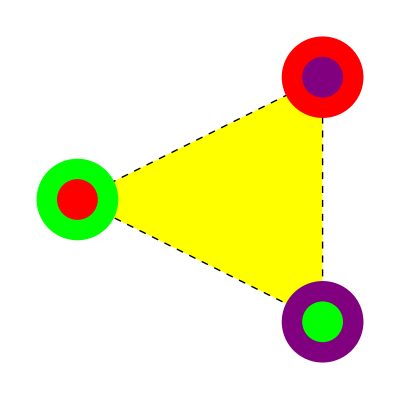

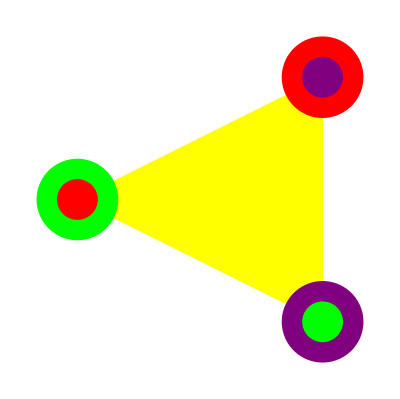

```mathematica
Graphics[{
{EdgeForm[Dashed],Yellow, Triangle[{{0,0},{2,-1},{2,1}}]},
{Green, Disk[{0,0},1/3]},
{Purple, Disk[{2,-1},1/3]},
{Red, Disk[{2,1},1/3]},
{Red, Disk[{0,0},1/6]},
{Green, Disk[{2,-1},1/6]},
{Purple, Disk[{2,1},1/6]}
}]
```

## 3. naloga [5 točk]

a) Napišite  funkcijo ‘krog’, ki  bo  sprejela  število ‘r’ in izračunala numerično vrednost obsega in ploščine kroga s polmerom ‘r’. Rezultat naj se izpiše v obliki:
“Obseg kroga s polmerom r=[r] je [obseg], ploščina pa [ploscina].”,
kjer [r] nadomestite z vnešeno vrednostjo polmera, [obseg] in [ploscina] pa z numerično vrednostjo obsega oz. ploščine pri vnešenem ‘r’ na 7 decimalk natančno (po decimalni piki naj se izpiše še 7 mest). Izračunajte 'krog[5/6]'.

```mathematica
krog[r_]:="Obseg kroga s polmerom r="<>ToString[r]<>" je "<>ToString[N[2Pi r,7]]<>", ploščina pa "<>ToString[N[Pi r^2,7]]<>"."
```

```mathematica
krog[5/6]
```

Obseg kroga s polmerom r=5
-
6 je 5.235988, ploščina pa 2.181662.

b) S pomočjo ‘RecurrenceTable’ izračunajte prvih 10 členov rekurzivnega zaporedja , z začetnim členom  in , in jih shranite v seznam ‘zaporedje’.  Rezultat čim bolj poenostavite. Nato izračunajte vsoto vseh elementov seznama ‘zaporedje’.

```mathematica
zaporedje = FullSimplify[RecurrenceTable[{x[n+1]==x[n]-4x[n-1],x[1]==a,x[2]==1/2},x,{n,1,10}]]
```

{a,1/2,1/2-4 a,-3/2-4 a,-7/2+12 a,5/2+28 a,33/2-20 a,13/2-132 a,-119/2-52 a,-171/2+476 a}

```mathematica
Total[zaporedje]
```

-247/2+305 a

c) Definirajte funkcijo ‘funZaporedje’, ki sprejme števili m in n med 1 in 10 ter vrne  (tj. razmerje med m-tim in n-tim členom zaporedja iz b)). Izračunjate ‘funZaporedje [8,9]’ za .

```mathematica
funZaporedje[m_,n_]:=zaporedje[[m]]/zaporedje[[n]]
```

```mathematica
funZaporedje [8,9]/.a->1/3
```

225/461

## 4. naloga [3 točke]

a) Definirajte seznam ‘planeti’ naših 8 planetov. Lahko si pomagate z uporabo naravnega jezika.

```mathematica
planeti = PlanetData[]
```

```mathematica
{Entity["Planet","Mercury"],Entity["Planet","Venus"],Entity["Planet","Earth"],Entity["Planet","Mars"],Entity["Planet","Jupiter"],Entity["Planet","Saturn"],Entity["Planet","Uranus"],Entity["Planet","Neptune"]}(*Pluton*)
```

b) Definirajte seznam , ki bo vseboval 8 trojic oblike {ime planeta, število lun planeta, masa planeta} za vsakega izmed 8 planetov iz seznama ‘planeti’, definiranega v točki a).

```mathematica
{#,PlanetData[#,"MoonCount"],PlanetData[#,"Mass"]}&/@planeti
```

{{Mercury,0 moons,3.3×10^23 kg},{Venus,0 moons,4.867×10^24 kg},{Earth,1 moons,5.97×10^24 kg},{Mars,2 moons,6.417×10^23 kg},{Jupiter,95 moons,1.898×10^27 kg},{Saturn,274 moons,5.683×10^26 kg},{Uranus,29 moons,8.681×10^25 kg},{Neptune,14 moons,1.024×10^26 kg}}

```mathematica
(*{Pluton, 5 moons,1305×10^22 kg}*)
```